```mathematica
(* IMPORT MODULES *)
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
On[Assert]
```

```mathematica
(* INITIALIZING PARAMETERS *)
uq=0.315 (* up quark mass *);
sq=0.577 (* strange quark mass *);
cq=1.836(* charm quark mass *);
bq=5.227 (* bottom quark mass *);
sigma=0.1653; (* coefficient of string strength term *)
alphaCoulomb=0.5069; (* coefficient of Coulomb term (0.0175) if you want to replicate Roberts *)
Cqqq=-0.8321(* V = -Subscript[α, C]/r + σr + Subscript[C, qqq] *);
κp=1.8609(* Thing in the spin term *);
CF=1/2(* Colour Factor *);
```

```mathematica
(* THIS FUNCTION RETURNS THE BARYON HAMILTONIAN FOR A GIVEN ω *)
ClearAll[Hb]
Hb[J_,P_,Isospin_,Λ_,γMax_,omega_,m1_,m2_,m3_,project_]:=Hb[J,P,Isospin,Λ,γMax,omega,m1,m2,m3,project]=(
ω=omega;
projector=Projector[J,P,Λ,γMax,Isospin];
sM=stateMatrix[J,P,Λ,γMax];
vCoulomb=polynomialOperatorRho[sM,-1];
vLinear=polynomialOperatorRho[sM,1];
spinPart12=(8 Pi)/(3m1 m2 r0[m1,m2]^3 Pi^(3/2))κp*GaussOperator[sM,ω,3,m1,m2,m3];
spinPart23=(8 Pi)/(3m2 m3 r0[m2,m3]^3 Pi^(3/2))κp*Transpose[t1].GaussOperator[sM,ω,1,m1,m2,m3].t1;
spinPart31=(8 Pi)/(3m3 m1 r0[m3,m1]^3 Pi^(3/2))κp*Transpose[t2].GaussOperator[sM,ω,2,m1,m2,m3].t2;

v12baryon=-alphaCoulomb*α[m1,m2,ω]*vCoulomb+(sigma*vLinear)/α[m1,m2,ω]+spinPart12;
v23baryon=-alphaCoulomb*α1[m1,m2,m3,ω]*(Transpose[t1].vCoulomb.t1)+(sigma*(Transpose[t1].vLinear.t1))/α1[m1,m2,m3,ω]+spinPart23;
v31baryon=-alphaCoulomb*α2[m1,m2,m3,ω]*(Transpose[t2].vCoulomb.t2)+(sigma*(Transpose[t2].vLinear.t2))/α2[m1,m2,m3,ω]+spinPart31;
kin=kMatrix[sM,omega,m1,m2,m3];
mas1=IdentityMatrix[size]*m1;
mas2=IdentityMatrix[size]*m2;
mas3=IdentityMatrix[size]*m3;
cqqq=IdentityMatrix[size]*(Cqqq);
kinetic=mas1+mas2+mas3+kin;
Hbaryon=kinetic+CF(v12baryon+v23baryon+v31baryon+3*cqqq);
If[project,Hbaryon=ApplyProjector[Hbaryon,projector]];
Return[Hbaryon]
)
```

```mathematica
(* INITIALISE HYPERPARAMETERS AND OBTAIN LOWEST LYING STATE *)

(**** !!!TUNABLE PARAMETERS!!! ****)
(**** !!!TUNABLE PARAMETERS!!! ****)
J=1/2;(* Total angular momentum J = Λ + S *)
P=+1;(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
Isospin=0;(* Isospin *)
γMax=8;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
Λ=0;(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
m1=uq;(* mass of quark 1 *)
m2=uq;(* mass of quark 2 *)
m3=cq;(* mass of quark 3 *)
rangeMin=0.5;
rangeMax=0.7;
increment=0.01;
save=False;(* Do you want to save the data? *)
(**** !!!END OF TUNABLE PARAMETERS!!! ****)
(**** !!!END OF TUNABLE PARAMETERS!!! ****)

(* Define Subscript[r, 0] parameter, see Silvestre's 1996 paper. Potential: AL1 *)
r0[mi_,mj_]:=1.6553((2mi mj)/(mi+mj))^-0.2204(* Gaussian function parameter *);

(* Choose to project depending if m1=m2 or m1≠m2, True and False, respectively *)
If[m1==m2,project=True,project=False];

(* Obtain projector matrix *)
projector=Projector[J,P,Λ,γMax,Isospin];

(* Calculate generalised transformation matrices *)
t1=tMatrix[J,P,Λ,γMax,m1,m2,m3,1];
t2=tMatrix[J,P,Λ,γMax,m1,m2,m3,2];

(* Obtain size of basis from size of talmi matrices (Subscript[N, Q]) *)
size=Dimensions[t1][[1]];

(* If projector has been applied, find position of first non-zero eigenvalue, if not applied then it's 1 *)
If[project==True,firstNonZero=size-Total[Diagonal[projector]]+1,firstNonZero=1];
```

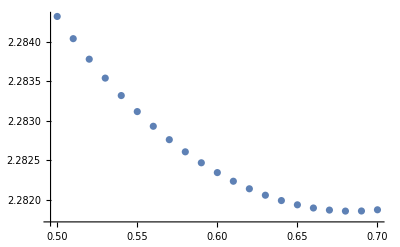

{6.85505,6.79625,6.76424,6.74467,6.66086,6.63612,6.58878,6.53724,6.50969,6.48115,6.2281,6.19668,6.1459,6.12499,6.07772,5.16835,5.11968,5.0552,5.03909,4.9563,4.89064,4.86908,4.83067,4.78844,4.76109,3.98834,3.96867,3.94105,3.88023,3.83168,3.67359,3.17827,3.13757,2.91266,2.29295,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Successfully Found Minimum

{0.68,2.28186}

```mathematica
(* Obtain a table of {{ω,E}} sets for varying ω to determine lowest Eigenvalue *)
tab=Table[{ω,Eigenvalues[Hb[J,P,Isospin,Λ,γMax,ω,m1,m2,m3,project]][[-firstNonZero]]-(2.02*10^-3)/(m1*m2*m3)},{ω,rangeMin,rangeMax,increment}];

(* Plot the list of above set of {{ω,E}} (The U-plot) *)
ListPlot[tab]

(* Extract ω's and Eigenvalues separately *)
omegas=tab[[All,1]];
evals=tab[[All,2]];
(* Find value of minimum eigenvalue *)
minEval=Min[evals];
(* Find positional index of minimum eigenvalue *)
posOfMinEval=Position[evals,minEval][[1,1]];
(* Use positional index of minimum eigenvalue to obtain the corresponding value of ω *)
optimumOmega=omegas[[posOfMinEval]];
(* Construct a list object containing {Subscript[ω, min],Subscript[E, min]} *)
minimum={optimumOmega,minEval};

(* Print all eigenvalues for all ω's *)
Print[Eigenvalues[Hb[J,P,Isospin,Λ,γMax,optimumOmega,m1,m2,m3,project]]//Chop]

(* Initiate an error counter, will go up by one for each error encountered *)
errors=0;
(* First, check if the list object {Subscript[ω, min],Subscript[E, min]} exists in the list of all {{ω,E}} *)
If[tab[[posOfMinEval]]!=minimum,errors+=1;Print["Does not agree"]]
(* Check if Subscript[E, min] is the first element of {{ω,E}}, if True, extend ω range to the left *)
If[posOfMinEval==1,errors+=1;Print["Need to extend range more to the left"]]
(* Check if Subscript[E, min] is the last element of {{ω,E}}, if True, extend ω range to the right *)
If[posOfMinEval==Length[tab],errors+=1;Print["Need to extend range more to the right"]]
(* Finally if no errors encountered print {Subscript[ω, min],Subscript[E, min]} *)
If[errors==0,Print["Successfully Found Minimum"];Print[minimum];]

(* Save data *)
If[save==True,
dirPath=FileNameJoin[{NotebookDirectory[],"lines/Silvestre/eigenValues"}];
quarkDict=Association[{uq->"u",sq->"s",cq->"c",bq->"b"}];
filename=quarkDict[m1]<>quarkDict[m2]<>quarkDict[m3]<>"/"<>"E"<>ToString[γMax]<>".mx";
fullPath=FileNameJoin[{dirPath,filename}];
Print["Successfully saved to:"];
Export[fullPath,tab]]
```

{0.4,0.5,0.6,0.7,0.8}

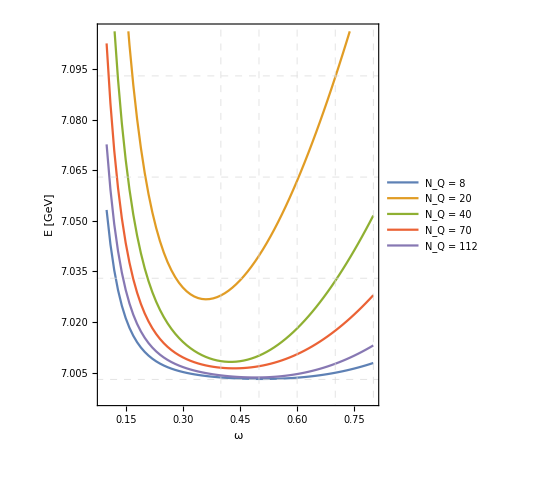

```mathematica
(* PLOTTING MASS PLOTS *)
allLinePaths=FileNames[All,"lines/Silvestre/eigenValues/scb"];
allFilenames=Table[FileNameJoin[{NotebookDirectory[],allLinePaths[[i]]}],{i,1,Length[allLinePaths]}];
allLinesData=Table[Import[allFilenames[[i]]],{i,1,Length[allFilenames]}];

plotRange={{0.09,0.8},Automatic};
frameTicks={{Automatic,None}, {Automatic,None}};
legendFontSize=14;
labelFontSize=14;
fontFamily="Times";
plotLegends={Placed[{Style["N_Q = 8",FontSize->legendFontSize,FontFamily->fontFamily],
Style["N_Q = 20",FontSize->legendFontSize,FontFamily->fontFamily],Style["N_Q = 40",FontSize->legendFontSize,FontFamily->fontFamily],
Style["N_Q = 70",FontSize->legendFontSize,FontFamily->fontFamily],
Style["N_Q = 112",FontSize->legendFontSize,FontFamily->fontFamily]
},{Center,Top}]};
labelStyle={FontSize->labelFontSize, FontFamily->fontFamily,Black};
frameLabel={{"E [GeV]",None},{"ω","Ω_cb, (scb)"}};
frame={{True,True},{True,True}};
vertGridLines=Table[7.003+x,{x,0,0.1,0.03}];
horzGridLines=Table[x,{x,0.4,0.8,0.1}]
gridLines={horzGridLines,vertGridLines};
gridLinesStyle=Directive[Dashed, LightGray];

plot=ListPlot[allLinesData,Joined->True,PlotRange->plotRange,
FrameTicks->frameTicks,
PlotLegends->plotLegends,
LabelStyle->labelStyle,
FrameLabel->frameLabel,
Frame->frame,
AspectRatio->1.2,
GridLines->gridLines,
GridLinesStyle->gridLinesStyle]
```

```mathematica
Export["plots/baryons/eigVals/scbEvsW.pdf",plot,"PDF","AllowRasterization"->False]
```

plots/baryons/eigVals/scbEvsW.pdf

{{0.05,0.000699556},{0.1,0.00187881},{0.15,0.00313284},{0.2,0.00424322},{0.25,0.00514767},{0.3,0.00586406},{0.35,0.00642949},{0.4,0.00687812},{0.45,0.00723705},{0.5,0.00752719},{0.55,0.00776476},{0.6,0.00796262},{0.65,0.00813106},{0.7,0.00827841},{0.75,0.00841131},{0.8,0.008535},{0.85,0.00865352},{0.9,0.00876992},{0.95,0.00888642},{1.,0.00900462},{1.05,0.0091256},{1.1,0.00925009},{1.15,0.00937852},{1.2,0.00951114},{1.25,0.00964804},{1.3,0.00978924},{1.35,0.00993467},{1.4,0.0100842},{1.45,0.0102378},{1.5,0.0103951}}

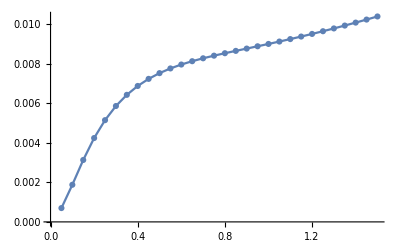

1.0702

```mathematica
sM=stateMatrix[J,P,Λ,γMax];
projector=Projector[J,P,Λ,γMax,Isospin];
observable=delta3RhoMatrix[sM];
(*r2=ApplyProjector[r2,projector];*)
eVec[omega_]:=(
ω=omega;
evec=Eigenvectors[Hb[J,P,Isospin,Λ,γMax,omega,m1,m2,m3,project]][[-firstNonZero]]//Chop
)
tab=Table[{om,(α[m1,m2,om]^3*eVec[om].observable.eVec[om])},{om,0.05,1.5,0.05}]
ListPlot[tab,Joined->True,PlotMarkers->Automatic,PlotRange->Automatic]
(α[m1,m2,minimum[[1]]]^3*eVec[minimum[[1]]].observable.eVec[minimum[[1]]])*5.068^3
```

```mathematica
√(3/2)*1.
```

1.22474

```mathematica
(0.56+0.39+0.53)/3
```

0.49

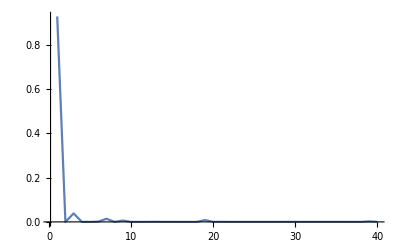

```mathematica
ListPlot[eVec[0.5]^2//Chop,PlotRange->All,Joined->True]
```

-Graphics3D-

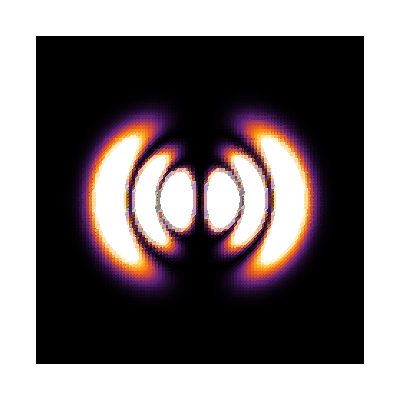

```mathematica
detail[n_,l_,m_]:=Total@{n,l,m};
wf[n_,l_,m_,ρ_,θ_,ϕ_]:=
Module[{},
radial=Rcoeff[n,l]*ρ^l*Exp[-ρ^2/2]*LaguerreL[n,l+1/2,ρ^2];
angular=SphericalHarmonicY[l,m,θ,ϕ];
Return[radial*Abs@angular]
];
orb[n_,l_,m_,x_,y_,z_]:=Module[{r=Norm@{x,y,z}},
wf[n,l,m,r,ArcCos@(z/r),ArcTan[x,0]]^2];
orbDensity[n_,l_,m_]:=DensityPlot[orb[n,l,m,x,0,z],{x,-detail[n,l,m],detail[n,l,m]},{z,-detail[n,l,m],detail[n,l,m]},
Mesh->False,Frame->False,PlotPoints->100,ColorFunctionScaling->True,ColorFunction->"SunsetColors"];
Plot3D[orb[2,2,2,1,y,z],{y,-2,2},{z,-2,2}]
orbDensity[2,2,2]
```

```mathematica
ev=Eigenvectors[Hb[J,P,Isospin,Λ,γMax,0.49,m1,m2,m3,project]][[-firstNonZero]]//Chop;
coeffs=ev^2;
basis=AddSpin[J,P,Λ,γMax];
qns=Table[basis[[n]][[1;;4]],{n,1,Length[basis]}];
qn1=qns[[1]]
orb
```

{0,0,0,0}